# Random Distribution by Selection Method

```mathematica
n = 10000;
xlist=Table[RandomReal[{-1,1}],{i, 1, n}];
ylist=Table[RandomReal[{0,1}],{i,1,n}];
xylist=Select[Table[If[ylist[[i]]>√(1-xlist[[i]]^2),{0,0},{xlist[[i]],ylist[[i]]}],{i,1,n}],# ≠ {0,0}&];
m=Length[xylist]
```

7880

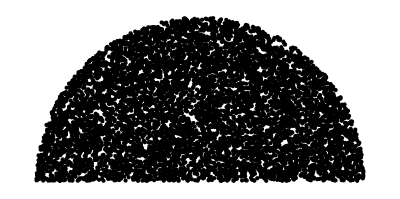

```mathematica
Graphics[{
Point[xylist]
}]
```

```mathematica
θlist=Table[ArcTan[xylist[[i,1]],xylist[[i,2]]] 180/π,{i,1,m}];
```

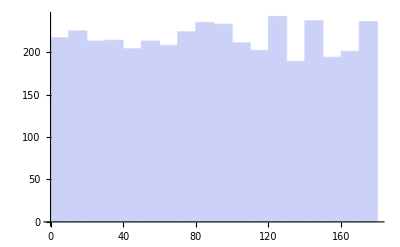

```mathematica
Histogram[θlist]
```

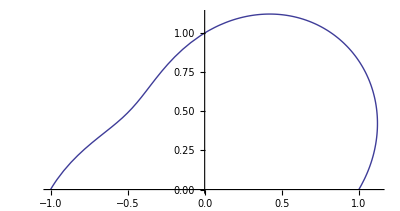

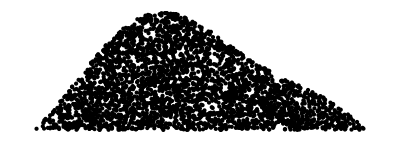

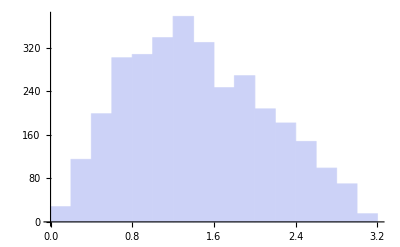

```mathematica
vlist=Table[{RandomReal[{0,π}],RandomReal[{0,2}]},{i,1,n}];
f[x_]:=(1+0.3Sin[2 x])
PolarPlot[f[x],{x,0,π}]
Svlist=
Select[
Table[
If[vlist[[i,2]]>f[vlist[[i,1]]]Sin[vlist[[i,1]]],{0,0},vlist[[i]]],{i,1,n}
],#≠{0,0}&];
m2=Length[Svlist];
Graphics[{
Point[Svlist]
}]
θlist=Table[Svlist[[i,1]],{i,1,m2}];
Histogram[θlist]
```

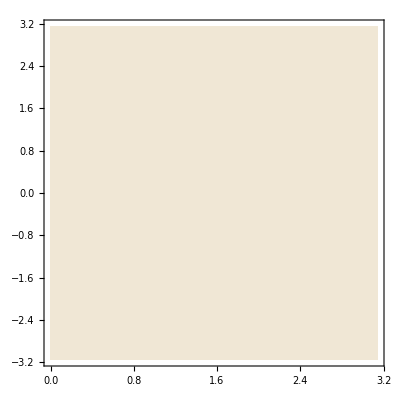

9811

-Graphics3D-

-Graphics3D-

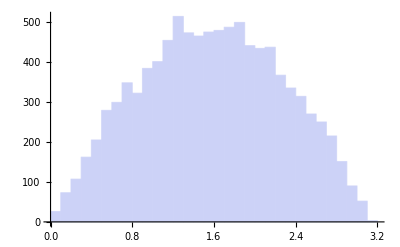

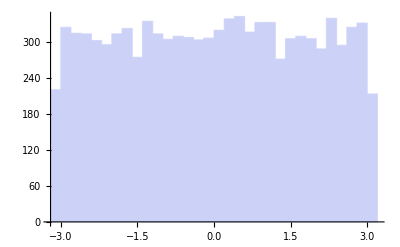

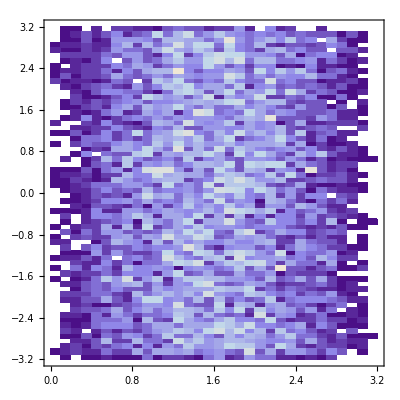

```mathematica
n=20000;
vlist=(* θ,ϕ,r *)Table[{RandomReal[{0,π}],RandomReal[{-π,π}],RandomReal[{0,1.3}]},{i,1,n}];
f[θ_,ϕ_]:=1
ContourPlot[f[θ,ϕ]Sin[θ],{θ,0,π},{ϕ,-π,π}]
Svlist=
Select[
Table[
If[vlist[[i,3]]>f[vlist[[i,1]],vlist[[i,2]]]Sin[vlist[[i,1]]],{0,0,0},vlist[[i]]],{i,1,n}
],#≠{0,0,0}&];
m2=Length[Svlist]
dpoint=Table[vlist[[i,3]]{Cos[vlist[[i,2]]]Sin[vlist[[i,1]]],Sin[vlist[[i,2]]]Sin[vlist[[i,1]]],Cos[vlist[[i,1]]]},{i,1,n}];
Sdpoint=Table[Svlist[[i,3]]{Cos[Svlist[[i,2]]]Sin[Svlist[[i,1]]],Sin[Svlist[[i,2]]]Sin[Svlist[[i,1]]],Cos[Svlist[[i,1]]]},{i,1,m2}];
SphericalPlot3D[{f[θ,ϕ],f[θ,ϕ]Sin[θ]},{θ,0,π},{ϕ,-π,π},PlotStyle->{Directive[Opacity[0.5],Red],Directive[Opacity[0.5],Blue]}]
Graphics3D[{
Arrow[{{0,0,0},{0,0,1.5}}],
Point[dpoint],
Red,Point[Sdpoint]
}]
θlist=Table[Svlist[[i,1]],{i,1,m2}];
ϕlist=Table[Svlist[[i,2]],{i,1,m2}];
Histogram[θlist]
Histogram[ϕlist]
DensityHistogram[
Table[{θlist[[i]],ϕlist[[i]]},{i,1,m2}],{{0.1},{0.1}}
]
```

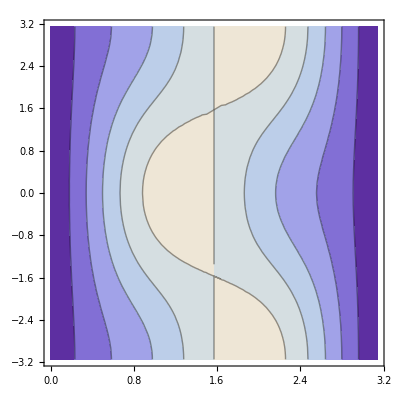

9731

-Graphics3D-

-Graphics3D-

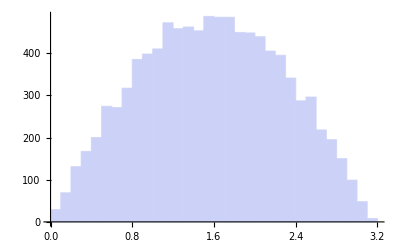

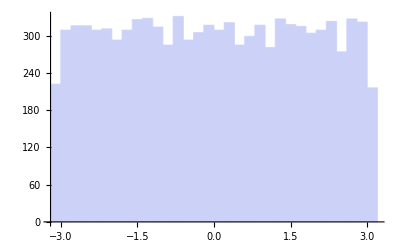

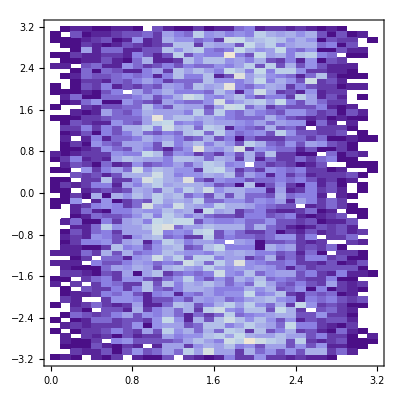

```mathematica
n=20000;
vlist=(* θ,ϕ,r *)Table[{RandomReal[{0,π}],RandomReal[{-π,π}],RandomReal[{0,1.3}]},{i,1,n}];
f[θ_,ϕ_]:=(1+0.3Sin[2 θ]Cos[ϕ])
ContourPlot[f[θ,ϕ]Sin[θ],{θ,0,π},{ϕ,-π,π}]
Svlist=
Select[
Table[
If[vlist[[i,3]]>f[vlist[[i,1]],vlist[[i,2]]]Sin[vlist[[i,1]]],{0,0,0},vlist[[i]]],{i,1,n}
],#≠{0,0,0}&];
m2=Length[Svlist]
dpoint=Table[vlist[[i,3]]{Cos[vlist[[i,2]]]Sin[vlist[[i,1]]],Sin[vlist[[i,2]]]Sin[vlist[[i,1]]],Cos[vlist[[i,1]]]},{i,1,n}];
Sdpoint=Table[Svlist[[i,3]]{Cos[Svlist[[i,2]]]Sin[Svlist[[i,1]]],Sin[Svlist[[i,2]]]Sin[Svlist[[i,1]]],Cos[Svlist[[i,1]]]},{i,1,m2}];
SphericalPlot3D[{f[θ,ϕ],f[θ,ϕ]Sin[θ]},{θ,0,π},{ϕ,-π,π},PlotStyle->{Directive[Opacity[0.5],Red],Directive[Opacity[0.5],Blue]}]
Graphics3D[{
Arrow[{{0,0,0},{0,0,1.5}}],
Point[dpoint],
Red,Point[Sdpoint]
}]
θlist=Table[Svlist[[i,1]],{i,1,m2}];
ϕlist=Table[Svlist[[i,2]],{i,1,m2}];
Histogram[θlist]
Histogram[ϕlist]
DensityHistogram[
Table[{θlist[[i]],ϕlist[[i]]},{i,1,m2}],{{0.1},{0.1}}
]
```